# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Packages (.m files)"];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

## Optimization algorithm

```mathematica
?GOOptimize
```

{ffinal,Mfinal,listStepSizeIterations,listfValues,listGradientNorms,metricG}=GOOptimize[f, df, Jinitial, listMinitial, {basisA, basisB}, {dimA, dimB}, tolerance, steplimit_:∞]

Optimization of a scalar function over the manifold of Gaussian states : 
The algorithm initializes at the starting points in Minitial in the manifold, each of which defines a trajectory for the optimization. 
At each multiple of 5 steps, the algorithm retains only the 20 % of the trajectories with the lowest function values and highest gradient 
norm, respectively. The optimization is terminated when the final remaining trajectory (or trajectories) first satisfies one of three stopping criteria : 
a lower bound on the gradient norm (tolerance), a limit on the number of iterations (steplimit), and a relative difference in function value below 10^-10

## Fundamental definitions and basic tools

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

GOΩqpqp[N] generates Ω in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOΩqqpp
```

GOΩqqpp[N] generates Ω in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOΩaabb
```

GOΩaabb[N] generates Ω in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOΩabab
```

GOΩabab[N] generates Ω in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

For Fermionic states

```mathematica
?GOGqpqp
```

GOGqpqp[N] generates G in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOGqqpp
```

GOGqqpp[N] generates G in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOGaabb
```

GOGaabb[N] generates G in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOGabab
```

GOGabab[N] generates G in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

Switching between structures

```mathematica
?GOTransformGtoJ
```

GOTransformGtoJ[G,'Gbasis','Jbasis'] generates J in Jbasis associated with G in Gbasis

```mathematica
?GOTransformΩtoJ
```

GOTransformΩtoJ[Ω,'Ωbasis','Jbasis'] generates J in Jbasis associated with Ω in Ωbasis

```mathematica
?GOTransformJtoG
```

GOTransformJtoG[J,'Jbasis','Gbasis'] generates G in Gbasis associated with J in Jbasis

```mathematica
?GOTransformJtoΩ
```

GOTransformJtoΩ[J,'Jbasis','Ωbasis'] generates Ω in Ωbasis associated with J in Jbasis

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases:
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

GOqqppFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMqqpp
```

GOqpqpFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMabab
```

GOaabbFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMaabb
```

GOababFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

GOababFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqpqp
```

GOaabbFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMqqpp
```

GOababFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqqpp
```

GOaabbFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

GOqpqpFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMabab
```

GOqqppFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMaabb
```

GOqpqpFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMaabb
```

GOqqppFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOSpBasis
```

SpBasis[N] generates Sp(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOSpBasisNoUN
```

spBasisNoUN[N] generates Sp(2N,R)/U(N) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOSpBasisNoU1
```

spBasisNoU1[N] generates Sp(2N,R)/U(1)^N Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOOBasis
```

OBasis[N] generates O(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
?GOPurifyStandardGBoson
```

G_sta=GOPurifyStandardGBoson[rlist,N,'Gform']
Constructs the bosonic purified state convariance matrix in the basis Gform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJBoson
```

J_sta=GOPurifyStandardJBoson[rlist,N,'Jform']
Constructs the bosonic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardΩFermion
```

Ω_sta=GOPurifyStandardΩFermion[rlist,N,'Ωform']
Constructs the fermionic purified state convariance matrix in the basis Ωform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJFermion
```

J_sta=GOPurifyStandardJFermion[rlist,N,'Jform']
Constructs the fermionic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

Tools for computational efficiency

```mathematica
?GOapproxExp
```

approxExp[ϵ,K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

logfunction[x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[x] calculates MatrixLog[x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

invMSp[m,'Mform'] inverts a symplectic matrix m in the basis Mform as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[{dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[Restriction] generates a function df[M,J_0,K] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

GOEoPgradFerm[Restriction] generates a function df[M,J_0,K] which calculates the gradient of the fermionic EoP for the given restriction with respect to the Lie algebra basis K

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[J_T] generates a function f[M,J_R0] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[J_T] generates a function df[M,J_R0,K] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[h] generates an energy function f[M,J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[h] generates an energy function f[M,J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples of applications

Bosonic Entanglement of Purification (EoP)

#### Preliminary definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### Example of the setup and execution for a typical optimization

1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,.1,1,0,3,3]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,6,"qpqp"];
```

3. Generate a list of the starting points for the optimization (in this case 50 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[12,"qpqp"]}}]//SparseArray,{50}];
```

4. Define the function and gradient for the optimization (in this case choosing an equal distribution of deg. of freedom in the ancillary)

```mathematica
Restriction=GORestrictionAA[{3,3,3,3}];
function=GOEoPBos[Restriction]; gradient=GOEoPgradBos[Restriction];
```

5. Execute the optimization

```mathematica
Result=GOOptimize[function,gradient,J0,M0List,{"None","GOSpBasis"},{6,6},10^-6,∞];
```

6. Evaluate the result

Final value: 0.379655

Number of iterations: 111

Number of total corrections: 85

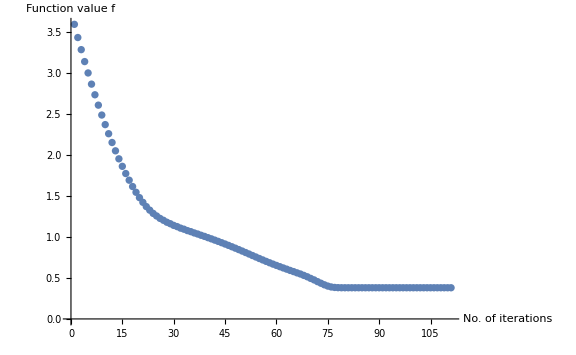

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```